2 - 10 ODEs reducible to Bessel’s ODE
This is just a sample of such ODEs; some more follow in the next problem set. Find a general solution in terms of J_v and J_-v or indicate when this is not possible. Use the indicated substitutions.

3.  x y''+y'+1/4 y=0  (√x=z)

```mathematica
Clear["Global`*"]
```

```mathematica
e1={x y''[x]+y'[x]+1/4 y[x]==0}
e2=DSolve[e1,y[x],x,Assumptions->{√x->z}]
```

{y[x]/4+y'[x]+x y''[x]==0}

{{y[x]→BesselJ[0,√x] C[1]+2 BesselY[0,√x] C[2]}}

The yellow expression above seems to include the text answer, but also a BesselY, which the text answer does not mention.

```mathematica
e2[[1,1,2]]
```

BesselJ[0,√x] C[1]+2 BesselY[0,√x] C[2]

```mathematica
gad=e2[[1,1,2]]/.{C[1]->1,C[2]->1}
```

BesselJ[0,√x]+2 BesselY[0,√x]

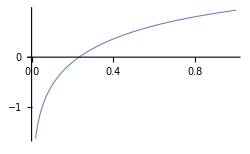

```mathematica
Plot[gad,{x,0,1},PlotRange->Automatic,PlotStyle->Thickness[0.003],ImageSize->250]
```

5.  Two-parameter ODE
x^2 y''+x y'+(λ^2 x^2-ν^2)y=0  (λx=z)

```mathematica
Clear["Global`*"]
```

```mathematica
e1={x^2 y''[x]+x y'[x]+(λ^2 x^2-ν^2) y[x]==0}
```

{(x^2 λ^2-ν^2) y[x]+x y'[x]+x^2 y''[x]==0}

```mathematica
e2=DSolve[e1,y,x,Assumptions->{λ x->z}]
```

{{y→Function[{x},BesselJ[ν,x λ] C[1]+BesselY[ν,x λ] C[2]]}}

Maybe including the assumptions keyword prevents the solution from being checked. The yellow cell above contains a Bessel function of the first kind and one of the second kind. The text answer contains the same Bessel of the first kind, but the other half is expressed as one independent from the first, not, that I can see, that it is one of the second kind.

```mathematica
glif=e2[[1,1]]/.{C[1]->1,C[2]->1,λ->2,ν->0}
```

y[x]→BesselJ[0,2 x]+BesselY[0,2 x]

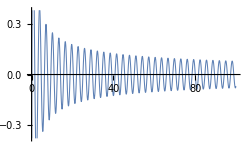

```mathematica
Plot[y[x]/.glif,{x,-100,100},PlotRange->Automatic,PlotStyle->Thickness[0.003],ImageSize->250]
```

7.  x^2 y''+x y'+1/4(x^2-1)y=0  (x=2z)

```mathematica
Clear["Global`*"]
```

```mathematica
e1={x^2 y''[x]+x y'[x]+1/4(x^2-1) y[x]==0}
```

{1/4 (-1+x^2) y[x]+x y'[x]+x^2 y''[x]==0}

```mathematica
e2=DSolve[e1,y[x],x,Assumptions->{x->2 z,x∈Reals}]
```

{{y[x]→(ⅇ^(-(ⅈ x)/2) C[1])/(√x)-(ⅈ ⅇ^((ⅈ x)/2) C[2])/(√x)}}

```mathematica
e3=ExpToTrig[e2]
```

{{y[x]→(C[1] Cos[x/2])/(√x)-(ⅈ C[2] Cos[x/2])/(√x)-(ⅈ C[1] Sin[x/2])/(√x)+(C[2] Sin[x/2])/(√x)}}

Mathematica gives the right answer, but includes imaginary elements, which, looking at the text answer, are not necessary.

```mathematica
e4=e3/.{-(ⅈ C[2] Cos[x/2])/(√x)->0,-(ⅈ C[1] Sin[x/2])/(√x)->0}
```

{{y[x]→(C[1] Cos[x/2])/(√x)+(C[2] Sin[x/2])/(√x)}}

```mathematica
e5=e4/.{C[1]->1,C[2]->1}
```

{{y[x]→Cos[x/2]/(√x)+Sin[x/2]/(√x)}}

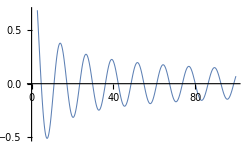

```mathematica
Plot[y[x]/.e5,{x,-100,100},PlotRange->Automatic,PlotStyle->Thickness[0.003],ImageSize->250]
```

9.  x y''+(2ν+1)y'+x y=0  (y=x^-ν u)

```mathematica
Clear["Global`*"]
```

```mathematica
e1={x y''[x]+(2 ν+1)y'[x]+x y[x]==0}
e2=DSolve[e1,y[x],x,Assumptions->{y[x]->x^-ν u}]
```

{x y[x]+(1+2 ν) y'[x]+x y''[x]==0}

{{y[x]→x^-ν BesselJ[ν,x] C[1]+x^-ν BesselY[ν,x] C[2]}}

The form of the above answer is not exactly the same as the text answer. I do not know if they are equal.

```mathematica
e3=e2/.{C[1]->1,C[2]->1}
```

{{y[x]→x^-ν BesselJ[ν,x]+x^-ν BesselY[ν,x]}}

```mathematica
e4=Simplify[e3,Assumptions->ν∉Integers]
```

{{y[x]→x^-ν (BesselJ[ν,x]+BesselY[ν,x])}}

```mathematica
e5=e4/.ν->.5
```

{{y[x]→((0.7978845608028654 Cos[1.5708-x])/(√x)-(0.7978845608028654 Sin[1.5708-x])/(√x))/x^0.5}}

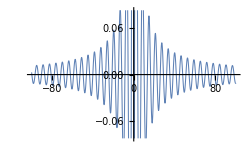

```mathematica
Plot[y[x]/.e5,{x,-100,100},PlotRange->Automatic,PlotStyle->Thickness[0.003],ImageSize->250]
```

19 - 25 Application of (21): deriviatives, integrals
Use the powerful formulas (21) to do problems 19 - 25.

23. Integration. Show that Integrate[x^2 J_0,x]=x^2 J_1[x]+x J_0[x]-Integrate[J_0[x],x]. (The last integral is nonelementary; tables exist, e.g. in reference [A13] in appendix 1.)